```mathematica
(* Evaluate this cell before doing anything else in order to define functions. *)

SetDirectory[NotebookDirectory[]];  (* Sets all path names to be relative to the directory where this notebook is. *)

(* Functions one can calculate on each time frame. *)
p[timeframe_]:=("data"/.timeframe)[[1]]
πp[timeframe_]:=("data"/.timeframe)[[2]]
q[timeframe_]:=("data"/.timeframe)[[3]]
πq[timeframe_]:=("data"/.timeframe)[[4]]
λ[timeframe_]:=("data"/.timeframe)[[5]]
πλ[timeframe_]:=("data"/.timeframe)[[6]]
τ[timeframe_]:=("time"/.timeframe)
α[timeframe_]:=1/(2πλ[timeframe])^2
v[timeframe_]:=p[timeframe]+τ[timeframe]
ρ[timeframe_]:=-1/2 Log[α[timeframe]]
l[timeframe_]:=p[timeframe]+1/2λ[timeframe]-3/2τ[timeframe]-Log[2]
Ptau[timeframe_]:=-πp[timeframe]/(2*πλ[timeframe])
Qtau[timeframe_]:=-Exp[-2p[timeframe]]πq[timeframe]/(2*πλ[timeframe])
λtau[timeframe_]:=1/(2*πλ[timeframe])^2(πp[timeframe]^2+Exp[-2p[timeframe]]πq[timeframe]^2+Exp[-2τ[timeframe]]spacederivative[p,timeframe]^2+Exp[2(p[timeframe]-τ[timeframe])]spacederivative[q,timeframe]^2)+Exp[(λ[timeframe]+2p[timeframe]+3τ[timeframe])/2]
Vtau[timeframe_]:=Ptau[timeframe]+1
ρtau[timeframe_]:=Exp[l[timeframe]]
A[timeframe_]:=Mean[-πp[timeframe]+2πλ[timeframe]+q[timeframe]*πq[timeframe]];
B[timeframe_]:=Mean[-πq[timeframe]];
c[tf_]:=Mean[(Qtau[tf]-2q[tf]+q[tf]Vtau[tf])2 πλ[tf]+q[tf](-πp[tf]+2πλ[tf]+q[tf]*πq[tf])];

(* Computes a finite-difference spatial derivative of a function on a time frame. *)
spacederivative=
Function[{f,timeframe},
Module[{temp,n,Δx},
temp=f[timeframe];
n=Length[temp];
Δx=2 Pi / n;
temp=Join[
{temp[[n-1]]},
{temp[[n]]},
temp,
{temp[[1]]},
{temp[[2]]}
];
Table[(2/3*(temp[[i+1]]-temp[[i-1]])+1/12*(temp[[i-2]]-temp[[i+2]]))/Δx,{i,1+2,n+2}]
]
];

(* Calculate the constraint. Note that this is pointwise in space. This should be identically 0 for solutions without error. *)
galconstraint[tf_]:=Module[{dp,dq,dλ},
 dp=spacederivative[p,tf];
 dq=spacederivative[q,tf];
 dλ=spacederivative[λ,tf];
(dp*πp[tf])+(dq*πq[tf])+(dλ*πλ[tf])
]
galconstraintavg[tf_]:=Mean[galconstraint[tf]]

(* More functions that can be computed on time frames. *)
Ev[tf_]:=Vtau[tf]^2+Exp[2(τ[tf]-ρ[tf])]spacederivative[p,tf]^2
Eq[tf_]:=Exp[2(v[tf]-τ[tf])](Qtau[tf]^2+Exp[2(τ[tf]-ρ[tf])]spacederivative[q,tf]^2)
En[tf_]:=Ev[tf]+Eq[tf]
J[tf_]:=1/2 En[tf]
mE[tf_]:=Mean[Exp[ρ[tf]-2τ[tf]] J[tf]]
Π[tf_]:=Mean[Exp[ρ[tf]] ]
Λ[tf_]:=1/2Mean[Exp[-2τ[tf]+ρ[tf]]Vtau[tf](v[tf]-Mean[v[tf]]-1)]
H[tf_]:=Π[tf](mE[tf]+Λ[tf])
Y[tf_]:=Mean[Exp[l[tf]+ρ[tf]+2τ[tf]]]
cc[tf_]:=Π[tf]Exp[-τ[tf]]H[tf]^(-1/2)
dd[tf_]:=Y[tf]Exp[-3τ[tf]]H[tf]^(-1/2)

ltau[tf_]:=-2-ρtau[tf]+1/2En[tf]

(* The terms from Beverly's superhamiltonian. The 'a' versions below just have an extra factor of 1/πλ so that they are O(1) generically. *)
H0[timeframe_]:=πp[timeframe]*πp[timeframe]/(4*πλ[timeframe])
Hkin[tf_]:=Exp[-2 p[tf]] πq[tf]*πq[tf]/(4*πλ[tf])
Hsmall[tf_]:=Exp[2 τ[tf]] spacederivative[p,tf]*spacederivative[p,tf]/(4*πλ[tf])
Hcurv[tf_]:=Exp[2 τ[tf]]Exp[2 p[tf]]spacederivative[q,tf]*spacederivative[q,tf]/(4*πλ[tf])
Htwist[tf_]:=πλ[tf] Exp[-3τ[tf]/2]Exp[λ[tf]/2+p[tf]]

H0a[timeframe_]:=πp[timeframe]*πp[timeframe]/(4*πλ[timeframe]*πλ[timeframe])
Hkina[tf_]:=Exp[-2 p[tf]] πq[tf]*πq[tf]/(4*πλ[tf]*πλ[tf])
Hsmalla[tf_]:=Exp[2 τ[tf]] spacederivative[p,tf]*spacederivative[p,tf]/(4*πλ[tf]*πλ[tf])
Hcurva[tf_]:=Exp[2 τ[tf]]Exp[2 p[tf]]spacederivative[q,tf]*spacederivative[q,tf]/(4*πλ[tf]*πλ[tf])
Htwista[tf_]:= Exp[-3τ[tf]/2]Exp[λ[tf]/2+p[tf]]

(* This is the function that takes a path to a json file and turns the result into a Mathematica-friendly form. DO NOT USE THIS FUNCTION DIRECTLY. Use the function apnp defined below instead. *)
myimport[path_]:=Block[{text,timeframes},
(* There is a bug with importing json floats of length greater than 19. See https://mathematica.stackexchange.com/questions/163825/problem-to-import-numbers-longer-than-19-digit-with-json-or-rawjson *)
Import[path,"Text"]//StringReplace[{"{"->"<|","}"->"|>",":"->"->","["->"{","]"->"}","e+"~~s_:>" 10^"~~s,"e-"~~s_:>" 10^-"~~s}]//ToExpression
]

(* Returns a nice (x,y) table after applying the function f to all the time frames. *)
ClearAll[pairs];
pairs[file_,f_]:=Block[{data,timeframes},
data=file//myimport;
 (* +++++++++++++++++++++++++++++++++++++
NOTA BENE: I use the operator // a lot in my coding.
The meaning is this: x//f//g == g[f[x]] analogous to the pipe | in *nix shells.
Closely related is the /* operator: f/*g is the function which is the composition of f and g.
That is, (f/*g)[x] = g[f[x]].
The difference is that f/*g can be passed around as a function, while f//g cannot; the latter must be applied to some input.
+++++++++++++++++++++++++++++++++++++ *)
timeframes=("evolution"/.data);
Table[{τ[i],f[i]},{i,timeframes}]//Sort[#,#1[[1]]<#2[[1]]&]&
]

(* Return a list of all the json files in the same directory as the input. *)
files=Function[file,
Module[{root,dir},
dir=DirectoryName[file];
root=FileBaseName[file];
FileNames[root<>".*.json",{dir}]
]
];

(*$HistoryLength=0;*)

(* The next few functions are related to actually getting data out of json files. Part of the complexity is related to memoization. There is the logic: 
  1) myimport gets data from a file and returns it as an array, but it doesn't memoize what is returned, so if we keep re-evaluating the same function on the same file, it takes the time to read the file from disk each time.
  2) pairshm is a memoized version of myimport: if we call it on the same file with the same function, it doesn't read the file again. The line <<"pairshm.mx"; reads previously memoized values from a file when we open the notebook again.
  3) The underlying files might change (as we evaluate for longer times) so we want to load them anew if they have changed, so pairsm gets the size and date of the file and makes pairshm get it again if these values have chaged.
  4) All the previous functions only act on a single file, but the data may be split up between many files. The function apnp looks for other files in the same directory for the given run and loads the data for all of them, then combines it and sorts by time. This is the function you should actually call to get a list of time frames.
*)

ClearAll[pairshm];
<<"pairshm.mx";
pairshm[file_,f_,size_,date_]:=pairshm[file,f,size,date]=Block[{data,timeframes},
PrintTemporary[file];
pairshm//DownValues//Map[#[[1]]&]//Select[StringMatchQ[ToString[#],___~~file~~___]&]//Select[StringMatchQ[ToString[#],___~~ToString[f]~~___]&]//Map[(#=.)&]; (* Clear previous memoizations for this function and file if they exist. *)
data=file//myimport;
timeframes=("evolution"/.data);
Table[{τ[i],f[i]},{i,timeframes}]
]

ClearAll[pairsm];
pairsm[file_,f_]:=pairshm[file,f,file//FileByteCount,file//FileDate//UnixTime];

files2=Function[file,
Module[{root,dir,reses,filenames},
dir=DirectoryName[file];
root=FileBaseName[file];
filenames=FileNames[root<>"_*.*.json",{dir}];
reses=filenames//Map[StringReplace[__~~"_"~~s__~~"."~~__~~".json":>s]]//Union//SortBy[ToExpression[#]&];
reses//Map[Select[filenames,StringMatchQ[dir~~root~~"_"~~#~~"."~~__~~".json"]]&]
]
];

ClearAll[apnp];
apnp[file_,f_]:=Block[{files,out},
files=files2[file]//Flatten;
out=Table[
j->pairsm[j,f]
,{j,files}]//Flatten[#,1]&;
(files2[file]/.out)//Map[Flatten[#,1]&]//Map[SortBy[#[[1]]&]]
]

dir="../long_runs/"; (* for the notebook, set the location where the runs are stored. Leave this as "../long_runs/" if you are running this notebook from the folder in the cloned git repo. *)
resolutions=Range[1,4]; (* Which resolutions to look for. 1 -> 512 , 2 -> 1024 , ... *)
twidth=6; (* When generating tables of plots, how many columns should there be? *)
```

41

{b0_0,gen_0,b0_9,b0_13,b0_24,b0_26,b0_43,b0_58,b0_61,b0_64,b0_81,b0_85,b0_89,b0_121,b0_139,b0_156,b0_162,b0_172,b0_179,b0_180,b0_190,gen_9,gen_13,gen_24,gen_43,gen_58,gen_61,gen_64,gen_69,gen_81,gen_85,gen_90,gen_121,gen_139,gen_156,gen_162,gen_163,gen_172,gen_179,gen_190,gen_192}

Part::partw: Part {1,2,3,4} of {{{0.,0.0431644},{0.0459996,-0.0695138},{0.0908831,-0.179517},{0.134619,-0.28698},{0.177197,-0.392023},{0.218619,-0.49476},{0.258901,-0.595293},«38»,{1.89184,-5.82512},{1.93288,-5.99715},{1.9737,-6.17089},{2.01427,-6.34617},{2.05455,-6.52286},«349»},{{0.,«20»},«50»}} does not exist.

ListPlot::lpn: {{{0.,0.0431644},{0.0459996,-0.0695138},{0.0908831,-0.179517},{0.134619,-0.28698},{0.177197,-0.392023},{0.218619,-0.49476},{0.258901,-0.595293},«38»,{1.89184,-5.82512},{1.93288,-5.99715},{1.9737,-6.17089},{2.01427,-6.34617},{2.05455,-6.52286},«349»},{«1»}}⟦{1,2,3,4}⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

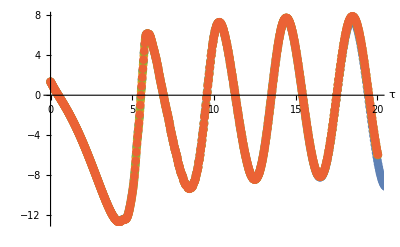
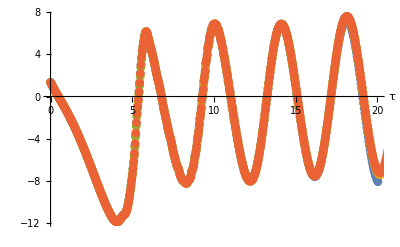
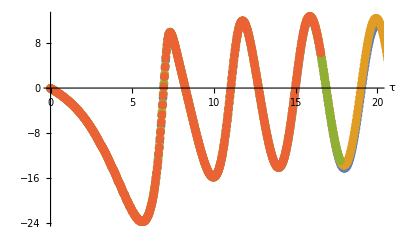
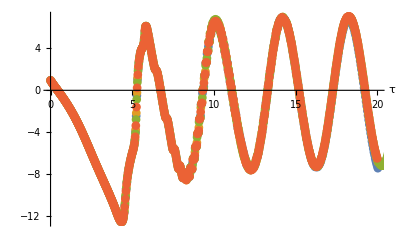
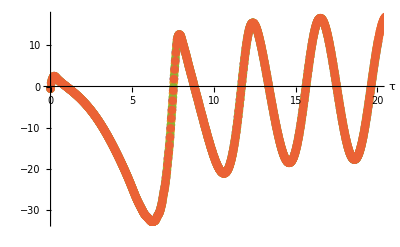
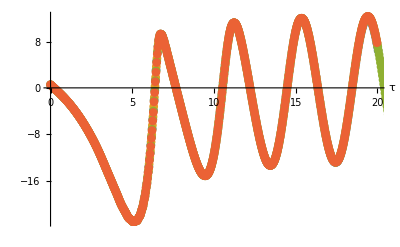
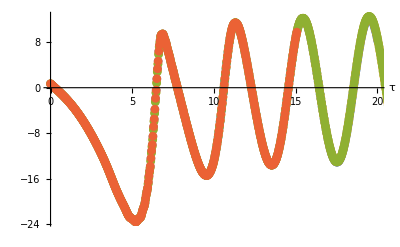
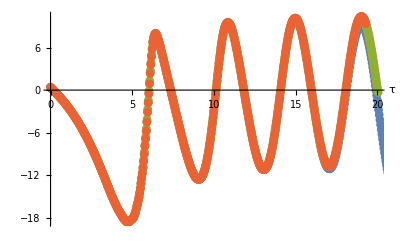
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | ListPlot[{{{0.,0.0431644},{0.0459996,-0.0695138},{0.0908831,-0.179517},{0.134619,-0.28698},{0.177197,-0.392023},{0.218619,-0.49476},{0.258901,-0.595293},{0.304483,-0.709923},{0.348589,-0.821826},{0.391268,-0.931131},{0.432578,-1.03796},{0.478184,-1.15716},{0.522163,-1.27344},{0.564598,-1.38694},{0.605571,-1.49779},{0.650018,-1.6195},{0.692821,-1.7382},{0.73408,-1.85404},{0.778225,-1.97958},{0.820696,-2.10196},{0.861602,-2.22136},{0.90491,-2.34944},{0.946568,-2.47429},{0.986686,-2.59609},{1.02881,-2.72569},{1.06935,-2.85206},{1.11159,-2.98552},{1.15222,-3.11563},{1.19429,-3.2522},{1.23475,-3.38532},{1.27643,-3.52435},{1.31652,-3.65988},{1.35764,-3.80081},{1.39962,-3.94671},{1.43996,-4.08888},{1.48102,-4.23562},{1.52266,-4.38653},{1.56268,-4.53362},{1.60319,-4.68458},{1.64407,-4.83908},{1.6852,-4.99683},{1.72651,-5.15754},{1.7679,-5.32095},{1.80929,-5.48683},{1.85063,-5.65495},{1.89184,-5.82512},{1.93288,-5.99715},{1.9737,-6.17089},{2.01427,-6.34617},{2.05455,-6.52286},{2.09573,-6.70632},{2.13647,-6.89069},{2.17676,-7.07584},{2.21767,-7.26679},{2.25803,-7.45808},{2.29883,-7.65444},{2.339,-7.85066},{2.37948,-8.05118},{2.42016,-8.25537},{2.46097,-8.46252},{2.501,-8.66754},{2.54107,-8.87406},{2.58111,-9.08128},{2.62179,-9.29236},{2.66228,-9.5027},{2.70254,-9.71186},{2.74317,-9.92277},{2.78346,-10.1315},{2.82397,-10.3406},{2.86404,-10.5466},{2.90422,-10.7519},{2.94442,-10.9557},{2.98459,-11.1568},{3.02467,-11.3541},{3.06507,-11.5478},{3.10525,-11.733},{3.1456,-11.9102},{3.18562,-12.079},{3.2257,-12.248},{3.26576,-12.4232},{3.30612,-12.6078},{3.34632,-12.7996},{3.38633,-12.9975},{3.42642,-13.2021},{3.46653,-13.412},{3.5066,-13.6256},{3.54685,-13.8409},{3.58694,-14.0508},{3.62708,-14.252},{3.6672,-14.4416},{3.70725,-14.6162},{3.74741,-14.7716},{3.78761,-14.8968},{3.82779,-14.9775},{3.86787,-15.039},{3.90802,-15.1304},{3.94817,-15.2531},{3.98826,-15.3954},{4.02841,-15.5481},{4.06855,-15.6971},{4.10862,-15.8243},{4.14873,-15.9176},{4.18882,-15.9567},{4.22882,-15.8991},{4.26883,-15.814},{4.30892,-15.8107},{4.34902,-15.8555},{4.38906,-15.9113},{4.42913,-15.9353},{4.46914,-15.8898},{4.50917,-15.6993},{4.54924,-15.4355},{4.58931,-15.3154},{4.6294,-15.2519},{4.66946,-15.156},{4.70952,-14.9407},{4.7496,-14.4786},{4.78965,-14.1468},{4.82969,-13.9446},{4.86975,-13.6965},{4.90975,-13.2201},{4.9498,-12.5676},{4.98983,-12.1935},{5.02985,-11.805},{5.06988,-11.0944},{5.10992,-10.3093},{5.14992,-9.8055},{5.18996,-9.11812},{5.22998,-8.02693},{5.27001,-7.34769},{5.31001,-6.51211},{5.35005,-5.24138},{5.39007,-4.43265},{5.4301,-3.24789},{5.4701,-2.02672},{5.5101,-1.06967},{5.55013,0.438584},{5.59017,1.37295},{5.63019,2.72647},{5.67022,3.6923},{5.71022,4.58428},{5.75024,5.55293},{5.79026,5.98919},{5.83027,6.66729},{5.87029,6.82839},{5.91032,6.89101},{5.95035,7.07758},{5.99035,6.9018},{6.03038,6.68083},{6.07041,6.58772},{6.11047,6.33998},{6.15048,5.99207},{6.19049,5.6763},{6.2305,5.45764},{6.27051,5.13666},{6.31054,4.75666},{6.35056,4.39681},{6.3906,4.11162},{6.43065,3.81041},{6.47068,3.43358},{6.51071,3.05463},{6.55073,2.71981},{6.59081,2.44057},{6.63082,2.08202},{6.67089,1.69758},{6.71092,1.33965},{6.75095,1.05274},{6.79097,0.713804},{6.83103,0.329582},{6.87105,-0.0356456},{6.9111,-0.326792},{6.95113,-0.66544},{6.99116,-1.05099},{7.03117,-1.40744},{7.07123,-1.68908},{7.11123,-2.0545},{7.15124,-2.43571},{7.19124,-2.73897},{7.23126,-3.06378},{7.27129,-3.44955},{7.31132,-3.76874},{7.35136,-4.07413},{7.39141,-4.45789},{7.43145,-4.75552},{7.47149,-5.07841},{7.51152,-5.45008},{7.55153,-5.70654},{7.59157,-6.07251},{7.63157,-6.37307},{7.67157,-6.67183},{7.7116,-7.01312},{7.7516,-7.26031},{7.79161,-7.60703},{7.83163,-7.8332},{7.87166,-8.16949},{7.91168,-8.38458},{7.9517,-8.69287},{7.9917,-8.91269},{8.03173,-9.14323},{8.07173,-9.41101},{8.11174,-9.57317},{8.15175,-9.83072},{8.19177,-10.0168},{8.23179,-10.1458},{8.27181,-10.3349},{8.31182,-10.5144},{8.35183,-10.6133},{8.39184,-10.6885},{8.43185,-10.7695},{8.47186,-10.8736},{8.51187,-10.948},{8.55187,-10.9757},{8.59188,-10.9727},{8.6319,-10.9446},{8.67191,-10.8922},{8.71192,-10.8128},{8.75192,-10.6985},{8.79194,-10.527},{8.83194,-10.3169},{8.87196,-10.1293},{8.91197,-9.9345},{8.95197,-9.67342},{8.99198,-9.29918},{9.03198,-9.01438},{9.07199,-8.61628},{9.112,-8.20231},{9.152,-7.76323},{9.192,-7.27826},{9.232,-6.71075},{9.27201,-6.22837},{9.31202,-5.60231},{9.35202,-4.94189},{9.39203,-4.31066},{9.43204,-3.67746},{9.47204,-2.98138},{9.51205,-2.25591},{9.55206,-1.51599},{9.59206,-0.767598},{9.63206,-0.0106904},{9.67206,0.767568},{9.71207,1.56155},{9.75207,2.28956},{9.79208,2.96868},{9.83208,3.63894},{9.87209,4.36077},{9.91209,4.9571},{9.95209,5.49557},{9.9921,6.08662},{10.0321,6.52593},{10.0721,6.93448},{10.1121,7.33989},{10.1521,7.59943},{10.1921,7.90358},{10.2321,8.05347},{10.2721,8.21197},{10.3121,8.28535},{10.3521,8.29942},{10.3921,8.30601},{10.4321,8.20672},{10.4721,8.13595},{10.5121,7.9472},{10.5521,7.79979},{10.5921,7.53911},{10.6321,7.32188},{10.6721,7.00577},{10.7121,6.72259},{10.7521,6.38126},{10.7921,6.02029},{10.8321,5.67499},{10.8721,5.24945},{10.9121,4.85307},{10.9522,4.45481},{10.9922,4.01291},{11.0322,3.54808},{11.0722,3.09971},{11.1122,2.64796},{11.1522,2.18744},{11.1922,1.71779},{11.2322,1.23996},{11.2722,0.755393},{11.3122,0.268659},{11.3522,-0.203417},{11.3922,-0.661703},{11.4322,-1.16211},{11.4722,-1.63107},{11.5122,-2.10452},{11.5522,-2.56212},{11.5922,-3.04735},{11.6322,-3.48847},{11.6722,-3.92591},{11.7122,-4.36289},{11.7522,-4.79337},{11.7922,-5.21824},{11.8322,-5.64059},{11.8722,-6.03986},{11.9122,-6.40153},{11.9522,-6.78768},{11.9922,-7.13312},{12.0322,-7.4533},{12.0722,-7.76462},{12.1122,-8.0638},{12.1522,-8.35215},{12.1922,-8.61563},{12.2322,-8.82718},{12.2722,-9.04961},{12.3122,-9.24288},{12.3522,-9.40028},{12.3922,-9.53571},{12.4322,-9.62363},{12.4722,-9.70489},{12.5122,-9.74478},{12.5522,-9.78445},{12.5922,-9.77317},{12.6322,-9.71578},{12.6722,-9.63542},{12.7122,-9.54236},{12.7522,-9.40565},{12.7922,-9.23129},{12.8322,-9.02699},{12.8722,-8.76289},{12.9122,-8.51413},{12.9523,-8.20882},{12.9923,-7.87236},{13.0323,-7.48082},{13.0723,-7.09865},{13.1123,-6.65614},{13.1523,-6.19895},{13.1923,-5.72709},{13.2323,-5.19269},{13.2723,-4.6736},{13.3123,-4.11541},{13.3523,-3.52663},{13.3923,-2.9569},{13.4323,-2.34212},{13.4723,-1.72521},{13.5123,-1.10168},{13.5523,-0.456698},{13.5923,0.186768},{13.6323,0.818513},{13.6723,1.4321},{13.7123,2.07273},{13.7523,2.67649},{13.7923,3.2793},{13.8323,3.84925},{13.8723,4.41278},{13.9123,4.93433},{13.9523,5.45035},{13.9923,5.93774},{14.0323,6.37347},{14.0723,6.78525},{14.1123,7.16585},{14.1523,7.52775},{14.1923,7.81353},{14.2323,8.08311},{14.2723,8.30604},{14.3123,8.50097},{14.3523,8.63682},{14.3923,8.74547},{14.4323,8.80301},{14.4723,8.8268},{14.5123,8.80552},{14.5523,8.75077},{14.5923,8.65054},{14.6323,8.53323},{14.6723,8.36305},{14.7123,8.16346},{14.7523,7.91617},{14.7923,7.65808},{14.8323,7.35874},{14.8723,7.02302},{14.9123,6.67538},{14.9523,6.29517},{14.9923,5.90795},{15.0323,5.48287},{15.0723,5.04219},{15.1123,4.58075},{15.1523,4.1102},{15.1923,3.60837},{15.2323,3.10652},{15.2723,2.60662},{15.3123,2.08532},{15.3523,1.5466},{15.3923,1.01364},{15.4323,0.485826},{15.4723,-0.0522025},{15.5123,-0.603013},{15.5523,-1.13244},{15.5923,-1.67306},{15.6323,-2.19123},{15.6723,-2.71485},{15.7123,-3.22547},{15.7523,-3.73581},{15.7923,-4.22993},{15.8323,-4.70491},{15.8723,-5.16179},{15.9123,-5.6142},{15.9523,-6.04698},{15.9923,-6.45609},{16.0323,-6.84019}},{{0.,0.0431644},{0.0459544,-0.0694034},{0.0907923,-0.179295},{0.134483,-0.286645},{0.177017,-0.391579},{0.218397,-0.494207},{0.258638,-0.594635},{0.304176,-0.709147},{0.348239,-0.820936},{0.39088,-0.930133},{0.432154,-1.03686},{0.477725,-1.15596},{0.51897,-1.26495},{0.56147,-1.37853},{0.602507,-1.48945},{0.644593,-1.60456},{0.685206,-1.71697},{0.726695,-1.8332},{0.766721,-1.94671},{0.807479,-2.06371},{0.848829,-2.18392},{0.890643,-2.30705},{0.930921,-2.4272},{0.971577,-2.55004},{1.01251,-2.67532},{1.05362,-2.80283},{1.09483,-2.93235},{1.13606,-3.06368},{1.17725,-3.19664},{1.21832,-3.33105},{1.25924,-3.46677},{1.29995,-3.60364},{1.34041,-3.74153},{1.38059,-3.88033},{1.42164,-4.02409},{1.46227,-4.16834},{1.50245,-4.313},{1.54323,-4.46185},{1.58346,-4.61078},{1.62412,-4.76343},{1.66417,-4.91588},{1.7045,-5.07162},{1.74503,-5.23036},{1.78567,-5.39186},{1.82634,-5.55588},{1.86699,-5.7222},{1.90754,-5.89062},{1.94795,-6.06097},{1.98817,-6.23307},{2.02881,-6.40963},{2.06914,-6.58752},{2.10973,-6.76934},{2.14991,-6.95211},{2.19022,-7.13832},{2.23058,-7.32768},{2.27094,-7.5199},{2.31122,-7.71467},{2.35138,-7.91167},{2.39182,-8.11282},{2.432,-8.31526},{2.47233,-8.52055},{2.51272,-8.72784},{2.5531,-8.93626},{2.59341,-9.14507},{2.6336,-9.35369},{2.67362,-9.56161},{2.71376,-9.77012},{2.75394,-9.9786},{2.7941,-10.1865},{2.83419,-10.3933},{2.87442,-10.5998},{2.91446,-10.804},{2.95451,-11.0065},{2.99453,-11.2061},{3.0347,-11.4027},{3.0747,-11.5929},{3.11472,-11.7754},{3.1549,-11.9498},{3.19497,-12.1181},{3.23507,-12.2883},{3.27514,-12.4653},{3.31531,-12.6509},{3.35532,-12.8435},{3.39547,-13.0437},{3.43553,-13.2493},{3.47559,-13.46},{3.5156,-13.6738},{3.55564,-13.8875},{3.59565,-14.0953},{3.63571,-14.2938},{3.67574,-14.4801},{3.71583,-14.6513},{3.75588,-14.801},{3.79597,-14.9174},{3.83603,-14.9895},{3.8761,-15.0547},{3.91613,-15.153},{3.95615,-15.2801},{3.9962,-15.4251},{4.03621,-15.578},{4.07621,-15.7235},{4.11623,-15.845},{4.15628,-15.93},{4.19629,-15.9545},{4.23636,-15.8787},{4.27642,-15.8076},{4.31648,-15.8166},{4.35654,-15.8662},{4.39654,-15.9193},{4.43654,-15.9333},{4.47655,-15.869},{4.51656,-15.6434},{4.55661,-15.4046},{4.59664,-15.302},{4.63664,-15.2396},{4.67665,-15.129},{4.71665,-14.878},{4.75667,-14.4004},{4.79669,-14.1073},{4.8367,-13.9089},{4.87671,-13.6374},{4.91673,-13.0903},{4.95675,-12.491},{4.99679,-12.1345},{5.0368,-11.7168},{5.07681,-10.9185},{5.11683,-10.2169},{5.15683,-9.71112},{5.19686,-8.93742},{5.23686,-7.89355},{5.27687,-7.23156},{5.31687,-6.29358},{5.35688,-5.09162},{5.39688,-4.28364},{5.43688,-2.96189},{5.47689,-1.8784},{5.51691,-0.850009},{5.55693,0.618811},{5.59693,1.54029},{5.63694,2.9616},{5.67696,3.8163},{5.71698,4.81862},{5.757,5.63222},{5.797,6.07788},{5.83702,6.72984},{5.87703,6.83311},{5.91706,6.92392},{5.95706,7.06405},{5.99708,6.86159},{6.03709,6.65273},{6.07711,6.56479},{6.11714,6.28382},{6.15717,5.93475},{6.19719,5.6323},{6.23722,5.41385},{6.27723,5.07406},{6.31726,4.69334},{6.35727,4.34178},{6.39727,4.07036},{6.43727,3.75045},{6.47728,3.36972},{6.51729,2.99525},{6.55731,2.6731},{6.59734,2.38658},{6.63737,2.01921},{6.67741,1.63625},{6.71742,1.28699},{6.75743,1.00479},{6.79745,0.652542},{6.83747,0.268056},{6.87747,-0.0891102},{6.91749,-0.373169},{6.95752,-0.726247},{6.99754,-1.11153},{7.03755,-1.45662},{7.07758,-1.7418},{7.11761,-2.11674},{7.15763,-2.49236},{7.19764,-2.78004},{7.23765,-3.12503},{7.27766,-3.50822},{7.31767,-3.80582},{7.35769,-4.13426},{7.3977,-4.51467},{7.43772,-4.79226},{7.47774,-5.13868},{7.51776,-5.49955},{7.55777,-5.75742},{7.59778,-6.13},{7.6378,-6.40169},{7.6778,-6.73066},{7.7178,-7.04708},{7.75781,-7.3167},{7.79782,-7.64585},{7.83783,-7.88731},{7.87785,-8.20443},{7.91785,-8.43796},{7.95786,-8.71195},{7.99787,-8.96497},{8.03788,-9.16089},{8.07789,-9.45334},{8.11791,-9.61796},{8.15792,-9.83084},{8.19793,-10.0572},{8.23794,-10.1864},{8.27794,-10.3284},{8.31794,-10.5328},{8.35795,-10.649},{8.39795,-10.7224},{8.43796,-10.783},{8.47796,-10.8465},{8.51797,-10.9165},{8.55797,-10.9611},{8.59798,-10.9653},{8.63799,-10.9364},{8.67799,-10.876},{8.71799,-10.7781},{8.758,-10.632},{8.798,-10.4635},{8.838,-10.3001},{8.878,-10.1275},{8.91801,-9.91153},{8.95801,-9.57029},{8.99801,-9.27578},{9.03801,-8.97786},{9.07802,-8.51975},{9.11802,-8.17072},{9.15803,-7.6445},{9.19803,-7.22892},{9.23803,-6.64642},{9.27803,-6.0868},{9.31804,-5.5441},{9.35804,-4.88568},{9.39804,-4.1963},{9.43804,-3.50318},{9.47805,-2.80963},{9.51805,-2.0987},{9.55805,-1.35839},{9.59805,-0.593739},{9.63805,0.175608},{9.67806,0.924946},{9.71806,1.64692},{9.75806,2.34927},{9.79806,3.06158},{9.83806,3.8091},{9.87807,4.43062},{9.91807,5.00936},{9.95807,5.64181},{9.99807,6.1297},{10.0381,6.57496},{10.0781,7.04023},{10.1181,7.34643},{10.1581,7.69193},{10.1981,7.90371},{10.2381,8.08204},{10.2781,8.23085},{10.3181,8.26932},{10.3581,8.33617},{10.3981,8.26562},{10.4381,8.23939},{10.4781,8.08106},{10.5181,7.96656},{10.5581,7.73493},{10.5981,7.54595},{10.6381,7.24924},{10.6781,7.00011},{10.7181,6.64835},{10.7581,6.3426},{10.7981,5.9699},{10.8381,5.58903},{10.8781,5.22269},{10.9181,4.78957},{10.9581,4.36138},{10.9981,3.94547},{11.0381,3.51415},{11.0781,3.05683},{11.1181,2.58001},{11.1581,2.10574},{11.1981,1.63315},{11.2381,1.16186},{11.2781,0.698071},{11.3181,0.227756},{11.3581,-0.264085},{11.3981,-0.76187},{11.4381,-1.21653},{11.4781,-1.70294},{11.5181,-2.17221},{11.5581,-2.64782},{11.5981,-3.08807},{11.6381,-3.55433},{11.6781,-4.01656},{11.7181,-4.45564},{11.7581,-4.88372},{11.7981,-5.29295},{11.8381,-5.67843},{11.8781,-6.08946},{11.9181,-6.46572},{11.9581,-6.83391},{11.9981,-7.16329},{12.0381,-7.49846},{12.0781,-7.81808},{12.1181,-8.10265},{12.1582,-8.37418},{12.1982,-8.64657},{12.2382,-8.85254},{12.2782,-9.08467},{12.3182,-9.25837},{12.3582,-9.41102},{12.3982,-9.54626},{12.4382,-9.64369},{12.4782,-9.70538},{12.5182,-9.7486},{12.5582,-9.77991},{12.5982,-9.76276},{12.6382,-9.69551},{12.6782,-9.6194},{12.7182,-9.50524},{12.7582,-9.37643},{12.7982,-9.19776},{12.8382,-8.96875},{12.8782,-8.72713},{12.9182,-8.43875},{12.9582,-8.14059},{12.9982,-7.78646},{13.0382,-7.41933},{13.0782,-7.01623},{13.1182,-6.59475},{13.1582,-6.1301},{13.1982,-5.61641},{13.2382,-5.12509},{13.2782,-4.57715},{13.3182,-4.01976},{13.3582,-3.44635},{13.3982,-2.83687},{13.4382,-2.21888},{13.4782,-1.6007},{13.5182,-0.988941},{13.5582,-0.335659},{13.5982,0.294856},{13.6382,0.933694},{13.6782,1.54964},{13.7182,2.18264},{13.7582,2.78068},{13.7982,3.38574},{13.8382,3.95324},{13.8782,4.51741},{13.9182,5.03772},{13.9582,5.55334},{13.9982,6.02118},{14.0382,6.47196},{14.0782,6.87052},{14.1182,7.25528},{14.1582,7.58876},{14.1982,7.88955},{14.2382,8.13817},{14.2782,8.36593},{14.3182,8.54712},{14.3582,8.68088},{14.3982,8.76983},{14.4382,8.83525},{14.4782,8.85034},{14.5182,8.83184},{14.5582,8.76681},{14.5982,8.6662},{14.6382,8.51491},{14.6782,8.34257},{14.7182,8.13361},{14.7582,7.90784},{14.7982,7.63092},{14.8382,7.33441},{14.8782,6.9949},{14.9182,6.64594},{14.9582,6.26},{14.9982,5.86172},{15.0382,5.43196},{15.0782,4.99507},{15.1182,4.53039},{15.1582,4.05797},{15.1982,3.5536},{15.2382,3.05105},{15.2782,2.54682},{15.3182,2.02458},{15.3582,1.48896},{15.3982,0.956926},{15.4382,0.422562},{15.4782,-0.118553},{15.5182,-0.647726},{15.5582,-1.19087},{15.5982,-1.71944},{15.6382,-2.24654},{15.6782,-2.75934},{15.7182,-3.27797},{15.7582,-3.77454},{15.7982,-4.26758},{15.8382,-4.74034},{15.8782,-5.19185},{15.9182,-5.64446},{15.9582,-6.0686},{15.9982,-6.47244},{16.0382,-6.85896}}}⟦{1,2,3,4}⟧,PlotRange→{{0,20},All},PlotStyle→PointSize[1/64],ImageSize→Scaled[1/6],Epilog→Inset[b0_156,ImageScaled[{0.8,0.2}]],AxesLabel→{τ,}] | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
Module[{type,filenames,runs,filess,k,print,i},
filenames=FileNames["*t_*.1.json",{dir}];
i=0;
runs=filenames//StringReplace[dir<>"t_"~~typeandnum__~~"_"~~__~~".json"->typeandnum]//Union//SortBy[ToExpression[#]&];
Print[runs//Length];
Print[runs];
Module[{tmp},
tmp=
Monitor[
Table[  (* For each run... *)
{
filee
,apnp[  (* ... get all the data from all the files ... *)
dir<>"t_"<>filee<>".json"
,{
galconstraint/*Abs/*Max/*Log10
,1/Π[#]Mean[Exp[ρ[#]]Ev[#]]&
,1/Π[#]Mean[Exp[ρ[#]]Eq[#]]&
,Mean[(l[#]-Log[1/2])]Exp[τ[#]/4]&
,Mean[(ρ[#]-τ[#]/2)Exp[ρ[#]]]/Mean[Exp[ρ[#]]]&
}[[4]] (* ... and apply the function I select from this little list ... *)
]//ListPlot[  (* ... then plot it ... *)
#[[resolutions]]
,PlotRange->{{0,20},All}
,PlotStyle->PointSize[1/64]
,ImageSize->Scaled[1/twidth ]
,Epilog->Inset[Framed[filee,Background->LightYellow],ImageScaled[{.8,.2}]] (* ... with a nice label of the name of the run ... *)
,AxesLabel->{"τ",""}
]&
}
,{filee,runs}
]
,{ProgressIndicator[FirstPosition[runs,filee][[1]]-1,{0,runs//Length},ImageSize->Scaled[1/2]],filee}];(*
tmp//Map[Export[#[[1]]<>"_rho.png",#[[2]],ImageSize->1000]&];*) (* uncomment the stuff to the left if you'd like to write images of the plots to the disk. *)
tmp//Map[#[[2]]&]
]//Partition[#,UpTo[twidth]]&//TableForm (* ... and make a nice grid of all the plots for the runs. *)
]
```